```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

## Important Snippets

```mathematica
Off[Part::partd]

Subscript[σ, F]=Function[{v},Evaluate[
Simplify[Max[
{v⟦1⟧,v⟦2⟧}.{x,y}/.Solve[Eliminate[D[{v⟦1⟧,v⟦2⟧}.{x,y}-λ(#⟦2⟧-#⟦1⟧&[Subscript[F, bdryCnds]]),{{x,y,λ}}]==0,λ],{x,y}]
],(v⟦1⟧|v⟦2⟧)∈Reals]
]]
γ_(F^°)=Subscript[σ, F];
(F^°)_bdryCnds=(γ_(F^°)[{x,y}]==1);
(𝒩̂)_(F^°)=Function[{ζ},Evaluate[
∇_{ζ⟦1⟧,ζ⟦2⟧} γ_(F^°)[{ζ⟦1⟧,ζ⟦2⟧}]
]]

On[Part::partd]
```

## Find optimal trajectory entering new medium

### Rotated Ellipse (Plain-Text Coding Example)

I did not plan to put this code in the paper but wrote this to show how the same results can be computed with unformatted function calls.

```mathematica
defVel[F0,ℛ[π/4].({Cos[t],2Sin[t]})]
defVel[F1,ℛ[-π/4].({Cos[t],2Sin[t]})+{1/10,1/5}]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

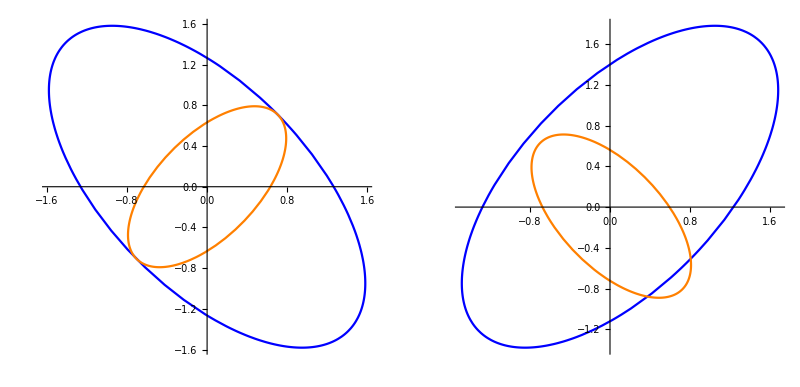

```mathematica
(* there are shorter ways to write this, but this should be descriptive *)
GraphicsRow[{
ParametricPlot[{
BoundaryParamerterization[F0],
BoundaryParamerterization[Polar[F0]]
},{t,0,2π},PlotStyle->{Blue,Orange}],
ParametricPlot[{
BoundaryParamerterization[F1],
BoundaryParamerterization[Polar[F1]]
},{t,0,2π},PlotStyle->{Blue,Orange}]
}]
```

```mathematica
(* example of getting exact outputs *)
Gauge[F0][{x,y}]
BoundaryConditions[F0]
```

1/2 √(x^2+y^2)

x^2+y^2==4

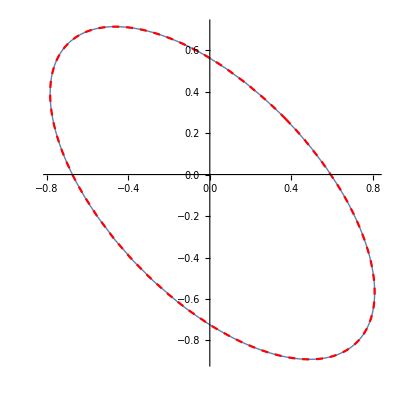
{2.08365×10^-12,{a→0.506967,b→1.0108,c1→0.0127066,c2→-0.0889462,t1→0.780327},-Graphics-}

```mathematica
{err,optimalRepresentation,comparisonPlot}=ClosedFormEllipse[Polar[F1],10]
```

```mathematica
(* example of doing algorithm *)
x0={0,-1};y0={1,0.};

(* anything below without a colon will print sequentially in the output cell *)
v0=(y0-x0)/Gauge[F0][y0-x0]
z0=NormalizedNormalCone[F0][v0]
l=z0[[1]];
z1s={l,#}&/@SolveValues[BoundaryConditions[Polar[F1]]/.x->l,y,Reals]
v1s=NormalizedNormalCone[Polar[F1]]/@z1s
v1s=Select[v1s,NonNegative@#[[2]]&]
```

{0.707107,0.707107}

{0.707107,0.707107}

{{0.707107,-0.822433},{0.707107,-0.190997}}

{{0.588325,-0.710078},{1.63105,0.802765}}

{{1.63105,0.802765}}

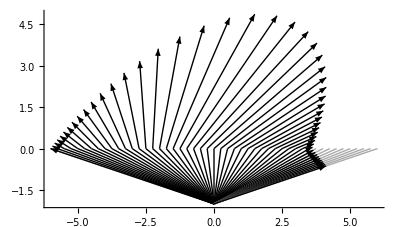

```mathematica
(* This algortithm can be looped over in a table to raycast multiple values *)
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0.,-2},T=4,t,y0,v0,ζ0,z1s,v1s},
(* set up y0 on parameterized Σ *)
y0={t0,0};

(* compute refraction according to optimality conditions *)
v0=(y0-x0)/Gauge[F0][y0-x0];
z0=NormalizedNormalCone[F0][v0];
l=z0[[1]];
z1s={l,#}&/@SolveValues[BoundaryConditions[Polar[F1]]/.x->l,y,Reals];
v1s=NormalizedNormalCone[Polar[F1]]/@z1s;
v1s=Select[v1s,NonNegative@#[[2]]&];

(* draw line in figure (wrapped by 'Graphics' call) *)
If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v1s
],
{t0,-6,6,0.25}
]},Axes->True]]
```

### Smooth Velocity

```mathematica
Clear[x,y]
defVel[F0,{x,y}.{x,y}==4]
defVel[F1,{x,y}.{x,y}==1]

x0={0,-1};xσ={1,0.};
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* v0 ∈ bdry(F0) *)
v0=(xσ-x0)/Subscript[γ, F0][xσ-x0]
```

{1.41421,1.41421}

```mathematica
(* ζ0 ∈ Subscript[N, F0](v0) s.t. γ_(F0^°)[ζ0]== 1 *)
ζ0=Subscript[𝒩̂, F0][v0]
```

{0.353553,0.353553}

```mathematica
(* ζ1 ∈ F1^° s.t. ζ1 + ζ0 ∈ Subscript[N, Σ](xσ), in this case Subscript[N, Σ](xσ) is the y-axis.
So the refreacted ζ1 must have the same tangent component as incident ζ0. *)
ℓ=ζ0⟦1⟧
ζ1s={ℓ,#}&/@SolveValues[(F1^°)_bdryCnds/.x->ℓ,y,Reals]
```

0.353553

{{0.353553,-0.935414},{0.353553,0.935414}}

```mathematica
(* v1 ∈ N_(F1^°)(ζ1) s.t. Subscript[γ, F1][v1]== 1 *)
v1s=(𝒩̂)_(F1^°)/@ζ1s
```

{{0.353553,-0.935414},{0.353553,0.935414}}

```mathematica
(* Select only velocities that enter M1 *)
v1s=Select[v1s,NonNegative@#[[2]]&]
```

{{0.353553,0.935414}}

### Polygonal Velocity

```mathematica
Clear[x,y]
defVel[F0,{{1,0},{0,1},{-1,0},{0,-1}}]
defVel[F1,{{1,1},{1,-1},{-1,1},{-1,-1}}]

x0={0,-1};xσ={1,0.};
LabeledPolarHullPlot/@{F0,F1}
```

{-Graphics-,-Graphics-}

```mathematica
(* v0 ∈ bdry(F0) *)
v0=(xσ-x0)/Subscript[γ, F0][xσ-x0]
```

{0.5,0.5}

```mathematica
(* ζ0 ∈ Subscript[N, F0](v0) s.t. γ_(F0^°)[ζ0]== 1 *)
ζ0=Subscript[𝒩̂, F0][v0]
```

{1,1}

```mathematica
(* ζ1 ∈ F1^° s.t. ζ1 + ζ0 ∈ Subscript[N, Σ](xσ), in this case Subscript[N, Σ](xσ) is the y-axis.
So the refreacted ζ1 must have the same tangent component as incident ζ0. *)
l=ζ0⟦1⟧;
ζ1s=Subscript[RefractedNormals, F1][ζ0]
```

{{1,0}}

```mathematica
(* v1 ∈ N_(F1^°)(ζ1) s.t. Subscript[γ, F1][v1]== 1 *)
v1s=(𝒩̂)_(F1^°)/@ζ1s
v1s=discretize/@v1s
```

{{1,1-2 λ}}

{{1,1},{1,1/2},{1,0},{1,-1/2},{1,-1}}

```mathematica
(* Select only velocities that enter M1 *)
v1s=Select[v1s,NonNegative@#[[2]]&]
```

{{1,1},{1,1/2},{1,0}}

Last::normal: Nonatomic expression expected at position 1 in Last[0].

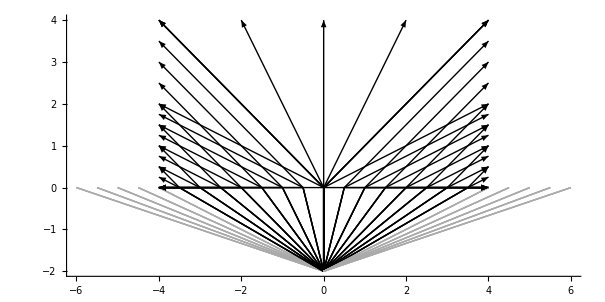

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-2},T=6,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
ζ0=Subscript[𝒩̂, F0][v0];
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}],{ζ2s}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-6,6,0.5}
]}],Axes->True]
```

## Finding Critical Velocity

```mathematica
Clear[x,y]
defVel[F1,({2Cos[t],Sin[t]}-{0,1/3})]
defVel[F0,({Cos[t],2Sin[t]}+{0,1/3})]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

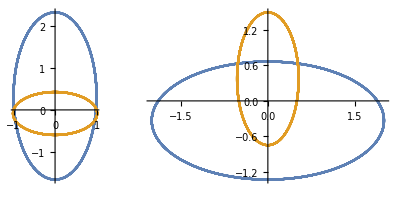

```mathematica
GraphicsRow[{
ParametricPlot[{Subscript[(F0), bdryParam],Subscript[(F0^°), bdryParam]},{t,-8 π,8 π}],ParametricPlot[{Subscript[(F1), bdryParam],Subscript[(F1^°), bdryParam]},{t,-8 π,8 π}]
}]
```

```mathematica
x0={0,-1};
Subscript[(F1), bdryCnds]
{lv1c,rv1c}={#,0}&/@SolveValues[Subscript[(F1), bdryCnds]/.{y->0},x]
{mlζ1c,mrζ1c}=Subscript[𝒩̂, F1]/@{lv1c,rv1c}

{lℓ,rℓ}={mlζ1c[[1]],mrζ1c[[1]]}
(* choosing Subscript[v, 0]^c *)
rζ0cy=Select[SolveValues[Subscript[(F0^°), bdryCnds]/.x->rℓ,y],Positive][[1]]
rζ0c={rℓ,rζ0cy}
rvc=(𝒩̂)_(F0^°)[rζ0c]
```

9 x^2+12 y (2+3 y)==32

{{-(4 √2)/3,0},{(4 √2)/3,0}}

{{-3/(4 √2),3/8},{3/(4 √2),3/8}}

{-3/(4 √2),3/(4 √2)}

3/280 (-8+3 √186)

{3/(4 √2),3/280 (-8+3 √186)}

{3/(4 √(2 (9/32+(9 (-8+3 √186)^2)/19600))),1/3+(3 (-8+3 √186))/(70 √(9/32+(9 (-8+3 √186)^2)/19600))}

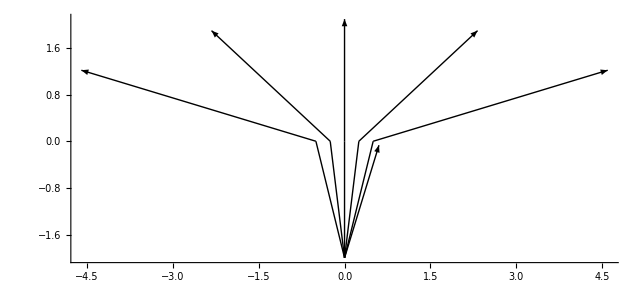

```mathematica
Show[{plt,Graphics[Arrow[{{0,-2},rvc+{0,-2}}]]}]
```

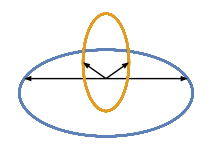

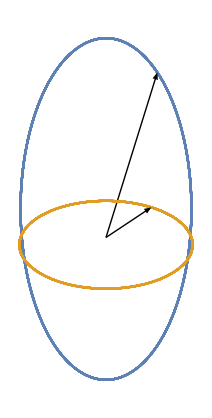

```mathematica
Show[{Graphics[Arrow[{{0,0},#}]&/@{lv1c,rv1c,mlζ1c,mrζ1c}],ParametricPlot[{Subscript[(F1), bdryParam],Subscript[(F1^°), bdryParam]},{t,-8 π,8 π}]
}]
Show[{Graphics[Arrow[{{0,0},#}]&/@{rζ0c,rvc}],ParametricPlot[{Subscript[(F0), bdryParam],Subscript[(F0^°), bdryParam]},{t,-8 π,8 π}]
}]
```

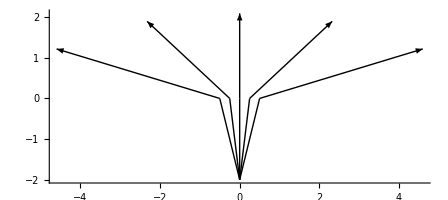

```mathematica
(* This algortithm can be looped over in a table to raycast multiple values *)
plt=Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0.,-2},T=4,t,y0,v0,ζ0,z1s,v1s},
(* set up y0 on parameterized Σ *)
y0={t0,0};

(* compute refraction according to optimality conditions *)
v0=(y0-x0)/Gauge[F0][y0-x0];
z0=NormalizedNormalCone[F0][v0];
l=z0[[1]];
z1s={l,#}&/@SolveValues[BoundaryConditions[Polar[F1]]/.x->l,y,Reals];
v1s=NormalizedNormalCone[Polar[F1]]/@z1s;
v1s=Select[v1s,NonNegative@#[[2]]&];

(* draw line in figure (wrapped by 'Graphics' call) *)
If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v1s
],
{t0,-6,6,0.25}
]},Axes->True]]
```

```mathematica
{nn,param}=FindMaximum[Subscript[(F1^°), bdryParam][[1]],t]
```

FindMaximum::nrnum: The function value -F1^° is not a real number at {t} = {1.}.

Set::shape: Lists {nn,param} and FindMaximum[(F1^°)_bdryParam⟦1⟧,t] are not the same shape.

FindMaximum::nrnum: The function value -F1^° is not a real number at {t} = {1.}.

FindMaximum[(F1^°)_bdryParam⟦1⟧,t]

## Hessian

```mathematica
defVel[F0,({Cos[t],2Sin[t]})]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

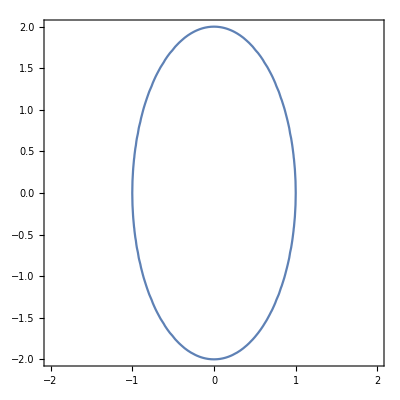

```mathematica
ContourPlot[Evaluate@BoundaryConditions[F0],{x,-2,2},{y,-2,2}]
```

```mathematica
Gauge[F0][{x,y}]
Hs=D[Gauge[F0][{x,y}],{{x,y}},{{x,y}}]
```

1/2 √(4 x^2+y^2)

{{-(8 x^2)/((4 x^2+y^2)^(3/2))+2/(√(4 x^2+y^2)),-(2 x y)/((4 x^2+y^2)^(3/2))},{-(2 x y)/((4 x^2+y^2)^(3/2)),-y^2/(2 (4 x^2+y^2)^(3/2))+1/(2 √(4 x^2+y^2))}}

```mathematica
Together[Hs]//MatrixForm
```

((2 y^2)/((4 x^2+y^2)^(3/2)) | -(2 x y)/((4 x^2+y^2)^(3/2))
-(2 x y)/((4 x^2+y^2)^(3/2)) | (2 x^2)/((4 x^2+y^2)^(3/2)))

```mathematica
Eigenvalues[Hs]
```

{0,(2 (x^2+y^2))/((4 x^2+y^2)^(3/2))}

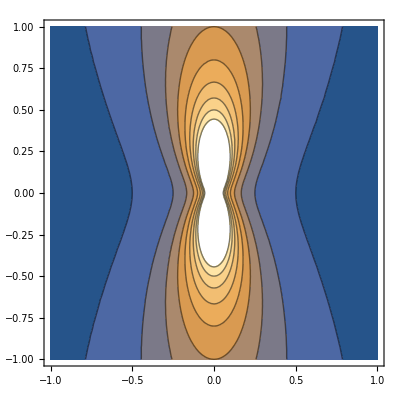

```mathematica
ContourPlot[(2 (x^2+y^2))/((4 x^2+y^2)^(3/2)),{x,-1,1},{y,-1,1}]
```

## Find optimal crossing point given destination

```mathematica
Clear[x,y]
defVel[F0,{x,y}.{x,y}==4]
defVel[F1,{x,y}.{x,y}==1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
x0={-1,-1};x1={1,1};

Clear[xσ]
Subscript[γ, F0][{xσ,0}-x0]+Subscript[γ, F1][x1-{xσ,0}]

FindMinimum[Subscript[γ, F0][{xσ,0}-x0]+Subscript[γ, F1][x1-{xσ,0}],xσ]
```

√(1+(1-xσ)^2)+1/2 √(1+(1+xσ)^2)

{2.01882,{xσ→0.538264}}

```mathematica
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
SolveValues[Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]==0,x]
%//N
```

-(1-x)/(√(1+(1-x)^2))+(1+x)/(2 √(1+(1+x)^2))

{1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))-1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))}

{0.538264}

```mathematica
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
x/.Solve[%==0,x]
xOpt=First@Select[%,Im[#]==0&]
%//N
```

-(1-x)/(√(1+(1-x)^2))+(1+x)/(2 √(1+(1+x)^2))

{1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))-1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))}

1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))-1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))

0.538264

## Trying to derive classic Snell

```mathematica
Subscript[F, bdryCnds]=({x,y}.{x,y}==a^2);
(*$Assumptions=a>0;*)
```

```mathematica
Sin[VectorAngle[{0,1},v0]]/Sin[VectorAngle[{0,1},v1s[[1]]]]
```

2.

```mathematica
x0={0,-1};xσ={a,0.};

v0=(xσ-x0)/Subscript[γ, F0][xσ-x0]
ζ0=Subscript[𝒩̂, F0][v0]
ζ1s=Subscript[RefractedNormals, F1][ζ0]
v1s=(𝒩̂)_(F1^°)/@ζ1s

Simplify[
Sin[VectorAngle[{0,1},v0]]/Sin[VectorAngle[{0,1},v1s[[1]]]]
]
```

{(2 a)/(√(1.+a^2)),2./(√(1.+a^2))}

{a/(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2))),1./(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2)))}

{{a/(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2))),ConditionalExpression[-1. √(1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))), ]},{a/(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2))),ConditionalExpression[√(1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))), ]}}

{{ConditionalExpression[a/(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2)) √(a^2/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))+1. (1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))))), ],ConditionalExpression[-(1. √(1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))))/(√(a^2/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))+1. (1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))))), ]},{ConditionalExpression[(1. a)/(√(1.+a^2) √(4./(1.+a^2)+(4 a^2)/(1.+a^2))), ],ConditionalExpression[1. √(1.-(1. a^2)/((1.+a^2) (4./(1.+a^2)+(4 a^2)/(1.+a^2)))), ]}}

2.

2.

```mathematica
Subscript[F, bdryCnds]=FullSimplify@Eliminate[Subscript[F, bdryParam][[1]]==x&&Subscript[F, bdryParam][[2]]==y,t];
```